We begin by defining some constants. The first relate to parameters used in the compressible KHRT case.

```mathematica
rho1 = 3.2*10^-7;
rho2 = 8*10^-8;
P = 200;
U1 = 20000;
U2 = 470000;
g = 10;
k = 1;
gammaval = 2.36414445322081*10^(-5)-45174.9728625431*I;
gammaval2 = 9.860132971832691*10^(-5)-1.700000000000000*10^(5)*I;
```

```mathematica
rho1in=8*10^-8;
rho2in= 3.2*10^-7;
U1in = 10000;
U2in=20000;
```

Now we define the functions we will be using

```mathematica
Csq[rho_,P_]:=P/rho;
gammabar[gamma_,k_,U_]:=gamma+I*k*U;
Lfun[g_,csq_]:=csq/g;
hpluss[L_,gammabar_,k_,csq_]:=(1/(2 L)+√(1/(4 L^2)+gammabar^2/csq+k^2));
hminuss[L_,gammabar_,k_,csq_]:=(1/(2 L)-√(1/(4 L^2)+gammabar^2/csq+k^2));
```

Since the perturbed velocity in z and the perturbed densities are related and have their own continuity conditions across the interface we must set the constants appropriately for consistent results

```mathematica
C1 = 1;
C2 = gammabar[gammaval,k,U2]/gammabar[gammaval,k,U1];
C3 = (-gammabar[gammaval,k,U1])/(Csq[rho1,P]*hminuss[Lfun[g,Csq[rho1,P]],gammabar[gammaval,k,U1],k,Csq[rho1,P]]);
C4 = C2* (-gammabar[gammaval,k,U2])/(Csq[rho2,P]*hpluss[Lfun[g,Csq[rho2,P]],gammabar[gammaval,k,U2],k,Csq[rho2,P]]);
```

```mathematica
N[C3]
```

0.0000350191-0.0000139339 ⅈ

```mathematica
N[C4]
```

0.0000350191-0.0000139339 ⅈ

```mathematica
N[C3-C4]
```

2.65807×10^-13+3.35379×10^-13 ⅈ

```mathematica
N[rho2/rho1*hminuss[Lfun[g,Csq[rho1,P]],gammabar[gammaval,k,U1],k,Csq[rho1,P]]/hpluss[Lfun[g,Csq[rho2,P]],gammabar[gammaval,k,U2],k,Csq[rho2,P]]*gammabar[gammaval,k,U2]^2/gammabar[gammaval,k,U1]^2]
```

1.-1.08754×10^-8 ⅈ

```mathematica
N[C4-(C3*Csq[rho1,P]/Csq[rho2,P]*hminuss[Lfun[g,Csq[rho1,P]],gammabar[gammaval,k,U1],k,Csq[rho1,P]]/hpluss[Lfun[g,Csq[rho2,P]],gammabar[gammaval,k,U2],k,Csq[rho2,P]]*gammabar[gammaval,k,U2]^2/gammabar[gammaval,k,U1]^2)]
```

-6.77626×10^-21+6.77626×10^-21 ⅈ

Original functions

```mathematica
w1t[rho1_,rho2_,P_,U1_,U2_,g_,k_,z_,t_,x_]:=Exp[z*hminuss[Lfun[g,Csq[rho1,P]],gammabar[gammaval,k,U1],k,Csq[rho1,P]]]*Exp[gammaval*t]*Exp[I*k*x];
w2t[rho1_,rho2_,P_,U1_,U2_,g_,k_,z_,t_,x_]:=Exp[z*hpluss[Lfun[g,Csq[rho2,P]],gammabar[gammaval,k,U2],k,Csq[rho2,P]]]*Exp[gammaval*t]*gammabar[gammaval,k,U2]/gammabar[gammaval,k,U1]*Exp[I*k*x];
δnt1[rho1_,rho2_,P_,U1_,U2_,g_,k_,z_,t_,x_]:=Exp[z*hminuss[Lfun[g,Csq[rho1,P]],gammabar[gammaval,k,U1],k,Csq[rho1,P]]]*Exp[gammaval*t]*Exp[I*k*x];
δnt2[rho1_,rho2_,P_,U1_,U2_,g_,k_,z_,t_,x_]:=Exp[z*hpluss[Lfun[g,Csq[rho2,P]],gammabar[gammaval,k,U2],k,Csq[rho2,P]]]*Exp[gammaval*t]*Exp[I*k*x]*rho2/rho1*hminuss[Lfun[g,Csq[rho1,P]],gammabar[gammaval,k,U1],k,Csq[rho1,P]]/hpluss[Lfun[g,Csq[rho2,P]],gammabar[gammaval,k,U2],k,Csq[rho2,P]]*gammabar[gammaval,k,U2]^2/gammabar[gammaval,k,U1]^2;
```

Functions with the defined constants

```mathematica
w1c[rho1_,rho2_,P_,U1_,U2_,g_,k_,z_,t_,x_]:=C1*Exp[z*hminuss[Lfun[g,Csq[rho1,P]],gammabar[gammaval,k,U1],k,Csq[rho1,P]]]*Exp[gammaval*t]*Exp[I*k*x];
w2c[rho1_,rho2_,P_,U1_,U2_,g_,k_,z_,t_,x_]:=C2*Exp[z*hpluss[Lfun[g,Csq[rho2,P]],gammabar[gammaval,k,U2],k,Csq[rho2,P]]]*Exp[gammaval*t]*Exp[I*k*x];
u1c[rho1_,rho2_,P_,U1_,U2_,g_,k_,z_,t_,x_]:=w1c[rho1,rho2,P,U1,U2,g,k,z,t,x]*(1/Lfun[g,Csq[rho1,P]]-hminuss[Lfun[g,Csq[rho1,P]],gammabar[gammaval,k,U1],k,Csq[rho1,P]])/(I*k+(I*gammabar[gammaval,k,U1]^2)/(k*Csq[rho1,P]));
u2c[rho1_,rho2_,P_,U1_,U2_,g_,k_,z_,t_,x_]:=w2c[rho1,rho2,P,U1,U2,g,k,z,t,x]*(1/Lfun[g,Csq[rho2,P]]-hpluss[Lfun[g,Csq[rho2,P]],gammabar[gammaval,k,U2],k,Csq[rho2,P]])/(I*k+(I*gammabar[gammaval,k,U2]^2)/(k*Csq[rho2,P]));

δnc1[rho1_,rho2_,P_,U1_,U2_,g_,k_,z_,t_,x_]:=C3*Exp[z*hminuss[Lfun[g,Csq[rho1,P]],gammabar[gammaval,k,U1],k,Csq[rho1,P]]]*Exp[gammaval*t]*Exp[I*k*x];
δnc2[rho1_,rho2_,P_,U1_,U2_,g_,k_,z_,t_,x_]:=C4*Exp[z*hpluss[Lfun[g,Csq[rho2,P]],gammabar[gammaval,k,U2],k,Csq[rho2,P]]]*Exp[gammaval*t]*Exp[I*k*x];
δρw1[rho1_,rho2_,P_,U1_,U2_,g_,k_,z_,t_,x_]:=rho1*Exp[-z/Lfun[g,Csq[rho1,P]]]*(gammabar[gammaval,k,U1]/(gammabar[gammaval,k,U1]^2+k^2*Csq[rho1,P]))*w1c[rho1,rho2,P,U1,U2,g,k,z,t,x]*(1/Lfun[g,Csq[rho1,P]]-hminuss[Lfun[g,Csq[rho1,P]],gammabar[gammaval,k,U1],k,Csq[rho1,P]]);
δρw2[rho1_,rho2_,P_,U1_,U2_,g_,k_,z_,t_,x_]:=rho2*Exp[z/Lfun[g,Csq[rho2,P]]]*(gammabar[gammaval,k,U2]/(gammabar[gammaval,k,U2]^2+k^2*Csq[rho2,P]))*w2c[rho1,rho2,P,U1,U2,g,k,z,t,x]*(1/Lfun[g,Csq[rho2,P]]-hpluss[Lfun[g,Csq[rho2,P]],gammabar[gammaval,k,U2],k,Csq[rho2,P]]);
δnw1[rho1_,rho2_,P_,U1_,U2_,g_,k_,z_,t_,x_]:=(gammabar[gammaval,k,U1]/(gammabar[gammaval,k,U1]^2+k^2*Csq[rho1,P]))*w1c[rho1,rho2,P,U1,U2,g,k,z,t,x]*(1/Lfun[g,Csq[rho1,P]]-hminuss[Lfun[g,Csq[rho1,P]],gammabar[gammaval,k,U1],k,Csq[rho1,P]]);
δnw2[rho1_,rho2_,P_,U1_,U2_,g_,k_,z_,t_,x_]:=(gammabar[gammaval,k,U2]/(gammabar[gammaval,k,U2]^2+k^2*Csq[rho2,P]))*w2c[rho1,rho2,P,U1,U2,g,k,z,t,x]*(1/Lfun[g,Csq[rho2,P]]-hpluss[Lfun[g,Csq[rho2,P]],gammabar[gammaval,k,U2],k,Csq[rho2,P]]);
```

```mathematica
N[δnw1[rho1,rho2,P,U1,U2,g,k,1,0.0001,0]]
```

0.0000732137+0.0000226765 ⅈ

```mathematica
N[δnc1[rho1,rho2,P,U1,U2,g,k,1,0.0001,0]]
```

0.0000732137+0.0000226765 ⅈ

```mathematica
N[δnt1[rho1,rho2,P,U1,U2,g,k,0,0,0]]
```

1.+0. ⅈ

```mathematica
N[δnw2[rho1,rho2,P,U1,U2,g,k,0,0,0]]
```

0.0000350191-0.0000139339 ⅈ

```mathematica
N[δnc2[rho1,rho2,P,U1,U2,g,k,0,0,0]]
```

0.0000350191-0.0000139339 ⅈ

```mathematica
N[δnt2[rho1,rho2,P,U1,U2,g,k,0,0,0]]
```

1.-1.08754×10^-8 ⅈ

```mathematica
N[δnw1[rho1,rho2,P,U1,U2,g,k,0,0,0]*rho2/rho1*hminuss[Lfun[g,Csq[rho1,P]],gammabar[gammaval,k,U1],k,Csq[rho1,P]]/hpluss[Lfun[g,Csq[rho2,P]],gammabar[gammaval,k,U2],k,Csq[rho2,P]]*gammabar[gammaval,k,U2]^2/gammabar[gammaval,k,U1]^2]
```

0.0000350191-0.0000139339 ⅈ

```mathematica
N[δnt1[rho1,rho2,P,U1,U2,g,k,0,0,0]*rho2/rho1*hminuss[Lfun[g,Csq[rho1,P]],gammabar[gammaval,k,U1],k,Csq[rho1,P]]/hpluss[Lfun[g,Csq[rho2,P]],gammabar[gammaval,k,U2],k,Csq[rho2,P]]*gammabar[gammaval,k,U2]^2/gammabar[gammaval,k,U1]^2]
```

1.-1.08754×10^-8 ⅈ

Here we plot the Density plot of the compressible RTKH instability

```mathematica
Manipulate[DensityPlot[((rho1*Exp[-z/Lfun[g,Csq[rho1,P]]]*(1+Re[δnc1[rho1,rho2,P,U1,U2,g,k,z,t,x]]))*UnitStep[z])+((rho2*Exp[-z/Lfun[g,Csq[rho2,P]]]*(1+Re[δnc2[rho1,rho2,P,U1,U2,g,k,z,t,x]]))*UnitStep[-z]*Sign[-z]),{x,-5,5},{z,-5,5},PlotLegends->Automatic,PlotRange->{Full,Full,{0,2*10^-6}}],{t,0.0005,0.001}]
```

Here we make the same plot but with contours instead

```mathematica
Manipulate[ContourPlot[((rho1*Exp[-z/Lfun[g,Csq[rho1,P]]]*(1+Re[δnc1[rho1,rho2,P,U1,U2,g,k,z,t,x]]))*UnitStep[z])+((rho2*Exp[-z/Lfun[g,Csq[rho2,P]]]*(1+Re[δnc2[rho1,rho2,P,U1,U2,g,k,z,t,x]]))*UnitStep[-z]*Sign[-z]),{x,-5,5},{z,-5,5},PlotLegends->Automatic,PlotRange->{Full,Full,{0,2*10^-6}},Contours->20],{t,0.5,1000000}]
```

```mathematica
Manipulate[ContourPlot[((rho1*Exp[-z/Lfun[g,Csq[rho1,P]]]*(Re[δnc1[rho1,rho2,P,U1,U2,g,k,z,t,x]]))*UnitStep[z])+((rho2*Exp[-z/Lfun[g,Csq[rho2,P]]]*(Re[δnc2[rho1,rho2,P,U1,U2,g,k,z,t,x]]))*UnitStep[-z]*Sign[-z]),{x,-6,6},{z,-5,5},PlotLegends->Automatic,Contours->20],{t,0.5,1000000}]
```

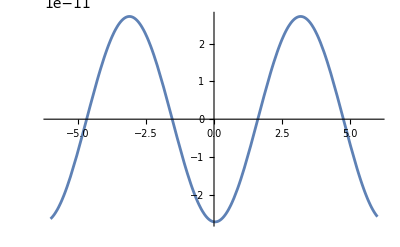

```mathematica
Plot[((rho1*Exp[2/Lfun[g,Csq[rho1,P]]]*(Re[δnc1[rho1,rho2,P,U1,U2,g,k,-2,1,x]]))*UnitStep[-2])+((rho2*Exp[2/Lfun[g,Csq[rho2,P]]]*(Re[δnc2[rho1,rho2,P,U1,U2,g,k,-2,1,x]]))*UnitStep[2]*Sign[2]),{x,-6,6}]
```

We now Look at only the perturbations

```mathematica
Manipulate[VectorDensityPlot[{{(U1+Re[u1c[rho1,rho2,P,U1,U2,g,k,z,t,x]])*UnitStep[z]+(U2+Re[u2c[rho1,rho2,P,U1,U2,g,k,z,t,x]])*UnitStep[-z]*Sign[-z],Re[w1c[rho1,rho2,P,U1,U2,g,k,z,t,x]*UnitStep[z]+w2c[rho1,rho2,P,U1,U2,g,k,z,t,x]*UnitStep[-z]*Sign[-z]]},((rho1*Exp[-z/Lfun[g,Csq[rho1,P]]]*(1+Re[δnc1[rho1,rho2,P,U1,U2,g,k,z,t,x]]))*UnitStep[z])+((rho2*Exp[-z/Lfun[g,Csq[rho2,P]]]*(1+Re[δnc2[rho1,rho2,P,U1,U2,g,k,z,t,x]]))*UnitStep[-z]*Sign[-z])},{x,-5,5},{z,-5,5},PlotLegends->Automatic,PerformanceGoal->"Quality",VectorScaling->Automatic,VectorColorFunctionScaling->False],{t,0,0.001}]
```

```mathematica
Manipulate[VectorDensityPlot[{{(U1+Re[u1c[rho1,rho2,P,U1,U2,g,k,z,t,x]])*UnitStep[z]+(U2+Re[u2c[rho1,rho2,P,U1,U2,g,k,z,t,x]])*UnitStep[-z]*Sign[-z],Re[w1c[rho1,rho2,P,U1,U2,g,k,z,t,x]*UnitStep[z]+w2c[rho1,rho2,P,U1,U2,g,k,z,t,x]*UnitStep[-z]*Sign[-z]]},((rho1*Exp[-z/Lfun[g,Csq[rho1,P]]]*(1+Re[δnc1[rho1,rho2,P,U1,U2,g,k,z,t,x]]))*UnitStep[z])+((rho2*Exp[-z/Lfun[g,Csq[rho2,P]]]*(1+Re[δnc2[rho1,rho2,P,U1,U2,g,k,z,t,x]]))*UnitStep[-z]*Sign[-z])},{x,-5,5},{z,-5,5},PlotLegends->BarLegend[{Automatic,{0,4*10^-7}}],ColorFunction->ColorData[{"TemperatureMap",{0,4*10^-7}}],ColorFunctionScaling->False,PerformanceGoal->"Quality",VectorScaling->Automatic,VectorColorFunctionScaling->False],{t,0,0.001}]
```

```mathematica
Range[0,4*10^-7,4*10^-7/20]
```

{0,1/50000000,1/25000000,3/50000000,1/12500000,1/10000000,3/25000000,7/50000000,1/6250000,9/50000000,1/5000000,11/50000000,3/12500000,13/50000000,7/25000000,3/10000000,1/3125000,17/50000000,9/25000000,19/50000000,1/2500000}

```mathematica
VideoGenerator[Rasterize@Show[ContourPlot[((rho1*Exp[-z/Lfun[g,Csq[rho1,P]]]*(1+Re[δnc1[rho1,rho2,P,U1,U2,g,k,z,#/25000,x]]))*UnitStep[z])+((rho2*Exp[-z/Lfun[g,Csq[rho2,P]]]*(1+Re[δnc2[rho1,rho2,P,U1,U2,g,k,z,#/25000,x]]))*UnitStep[-z]*Sign[-z]),{x,-5,5},{z,-5,5},Contours->{0,1/50000000,1/25000000,3/50000000,1/12500000,1/10000000,3/25000000,7/50000000,1/6250000,9/50000000,1/5000000,11/50000000,3/12500000,13/50000000,7/25000000,3/10000000,1/3125000,17/50000000,9/25000000,19/50000000,1/2500000},PlotLegends->BarLegend[{Automatic,{0,4*10^-7}}],ColorFunction->ColorData[{"Rainbow",{0,4*10^-7}}],ColorFunctionScaling->False,FrameLabel->{"x","z"},PlotRange->{Full,Full,{0,2*10^-6}},PerformanceGoal->"Quality"],VectorPlot[{(U1+Re[u1c[rho1,rho2,P,U1,U2,g,k,z,#/25000,x]])*UnitStep[z]+(U2+Re[u2c[rho1,rho2,P,U1,U2,g,k,z,#/25000,x]])*UnitStep[-z]*Sign[-z],Re[w1c[rho1,rho2,P,U1,U2,g,k,z,#/25000,x]*UnitStep[z]+w2c[rho1,rho2,P,U1,U2,g,k,z,#/25000,x]*UnitStep[-z]*Sign[-z]]},{x,-5,5},{z,-5,5},PlotLegends->BarLegend[{Automatic,{39000,130000}}],VectorColorFunctionScaling->False,VectorColorFunction->ColorData[{"GrayTones",{39000,130000}}]],VectorRange->{35000,140000}]&,20,RasterSize->{500,500},BitRate->10 Quantity[, ("Megabits")/("Seconds")],FrameRate->60]//Parallelize
```

```mathematica
Parallelize[VideoGenerator[Rasterize@Show[ContourPlot[((rho1*Exp[-z/Lfun[g,Csq[rho1,P]]]*(1+Re[δnc1[rho1,rho2,P,U2,U2,g,k,z,#/25000,x]]))*UnitStep[z])+((rho2*Exp[-z/Lfun[g,Csq[rho2,P]]]*(1+Re[δnc2[rho1,rho2,P,U2,U2,g,k,z,#/25000,x]]))*UnitStep[-z]*Sign[-z]),{x,-5,5},{z,-5,5},Contours->{0,1/50000000,1/25000000,3/50000000,1/12500000,1/10000000,3/25000000,7/50000000,1/6250000,9/50000000,1/5000000,11/50000000,3/12500000,13/50000000,7/25000000,3/10000000,1/3125000,17/50000000,9/25000000,19/50000000,1/2500000},PlotLegends->BarLegend[{Automatic,{0,4*10^-7}}],ColorFunction->ColorData[{"Rainbow",{0,4*10^-7}}],ColorFunctionScaling->False,FrameLabel->{"x","z"},PlotRange->{Full,Full,{0,2*10^-6}},PerformanceGoal->"Quality"],VectorPlot[{(U2+Re[u1c[rho1,rho2,P,U2,U2,g,k,z,#/25000,x]])*UnitStep[z]+(U2+Re[u2c[rho1,rho2,P,U2,U2,g,k,z,#/25000,x]])*UnitStep[-z]*Sign[-z],Re[w1c[rho1,rho2,P,U2,U2,g,k,z,#/25000,x]*UnitStep[z]+w2c[rho1,rho2,P,U2,U2,g,k,z,#/25000,x]*UnitStep[-z]*Sign[-z]]},{x,-5,5},{z,-5,5},PlotLegends->BarLegend[{Automatic,{39000,130000}}],VectorColorFunctionScaling->False,VectorColorFunction->ColorData[{"GrayTones",{39000,130000}}]],VectorRange->{35000,140000}]&,20,RasterSize->{500,500},BitRate->5 Quantity[, ("Megabits")/("Seconds")],FrameRate->30]]
```

```mathematica
VideoGenerator[Rasterize@Show[ContourPlot[((rho1*Exp[-z/Lfun[g,Csq[rho1,P]]]*(1+Re[δnc1[rho1,rho2,P,U1,U2,g,k,z,#/25000,x]]))*UnitStep[z])+((rho2*Exp[-z/Lfun[g,Csq[rho2,P]]]*(1+Re[δnc2[rho1,rho2,P,U1,U2,g,k,z,#/25000,x]]))*UnitStep[-z]*Sign[-z]),{x,-5,5},{z,-5,5},Contours->20,ColorFunction->"StarryNightColors",FrameLabel->{"x","z"},PlotRange->{Full,Full,{0,2*10^-6}},PlotLegends->Automatic],VectorPlot[{(U1+Re[u1c[rho1,rho2,P,U1,U2,g,k,z,#/25000,x]])*UnitStep[z]+(U2+Re[u2c[rho1,rho2,P,U1,U2,g,k,z,#/25000,x]])*UnitStep[-z]*Sign[-z],Re[w1c[rho1,rho2,P,U1,U2,g,k,z,#/25000,x]*UnitStep[z]+w2c[rho1,rho2,P,U1,U2,g,k,z,#/25000,x]*UnitStep[-z]*Sign[-z]]},{x,-5,5},{z,-5,5},VectorScaling->Automatic,PlotLegends->Automatic]]&,2,RasterSize->{500,500},BitRate->5 Quantity[, ("Megabits")/("Seconds")],FrameRate->10]//Parallelize
```

```mathematica
(*VideoGenerator[Rasterize@Plotfunction[#]&,10,RasterSize->{600,600},BitRate->10Quantity[, ("Megabits")/("Seconds")],FrameRate->60]//Parallelize*)
```

```mathematica
(*VideoGenerator[Rasterize@Plotfunction[#]&,10,RasterSize->{600,600},BitRate->5Quantity[, ("Megabits")/("Seconds")],FrameRate->30]//Parallelize*)
```

Here we only plot the perturbations

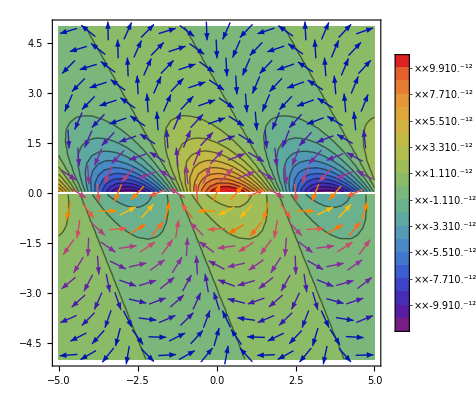

```mathematica
Show[ContourPlot[((rho1*Exp[-z/Lfun[g,Csq[rho1,P]]]*(Re[δnc1[rho1,rho2,P,U1,U2,g,k,z,0,x]]))*UnitStep[z])+((rho2*Exp[-z/Lfun[g,Csq[rho2,P]]]*(Re[δnc2[rho1,rho2,P,U1,U2,g,k,z,0,x]]))*UnitStep[-z]*Sign[-z]),{x,-5,5},{z,-5,5},PlotLegends->Automatic,PlotRange->{Full,Full,Full},Contours->20,ColorFunction->"Rainbow"],VectorPlot[{(Re[u1c[rho1,rho2,P,U1,U2,g,k,z,0,x]])*UnitStep[z]+(Re[u2c[rho1,rho2,P,U1,U2,g,k,z,0,x]])*UnitStep[-z]*Sign[-z],Re[w1c[rho1,rho2,P,U1,U2,g,k,z,0,x]*UnitStep[z]+w2c[rho1,rho2,P,U1,U2,g,k,z,0,x]*UnitStep[-z]*Sign[-z]]},{x,-5,5},{z,-5,5},PlotLegends->Automatic]]
```

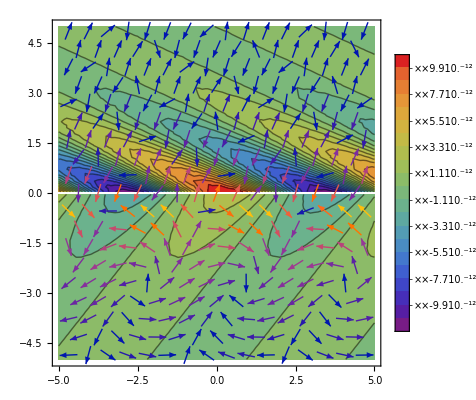

```mathematica
Show[ContourPlot[((rho1*Exp[-z/Lfun[g,Csq[rho1,P]]]*(Re[δnc1[rho1,rho2,P,0,0,g,k,z,0,x]]))*UnitStep[z])+((rho2*Exp[-z/Lfun[g,Csq[rho2,P]]]*(Re[δnc2[rho1,rho2,P,0,0,g,k,z,0,x]]))*UnitStep[-z]*Sign[-z]),{x,-5,5},{z,-5,5},PlotLegends->Automatic,PlotRange->{Full,Full,Full},Contours->20,ColorFunction->"Rainbow"],VectorPlot[{(Re[u1c[rho1,rho2,P,0,0,g,k,z,0,x]])*UnitStep[z]+(Re[u2c[rho1,rho2,P,0,0,g,k,z,0,x]])*UnitStep[-z]*Sign[-z],Re[w1c[rho1,rho2,P,0,0,g,k,z,0,x]*UnitStep[z]+w2c[rho1,rho2,P,U2,U2,g,k,z,0,x]*UnitStep[-z]*Sign[-z]]},{x,-5,5},{z,-5,5},PlotLegends->Automatic]]
```

```mathematica
Manipulate[ContourPlot[((rho1*Exp[-z/Lfun[g,Csq[rho1,P]]]*(Re[δnc1[rho1,rho2,P,U1,U2,g,k,z,t,x]]))*UnitStep[z])+((rho2*Exp[-z/Lfun[g,Csq[rho2,P]]]*(Re[δnc2[rho1,rho2,P,U1,U2,g,k,z,t,x]]))*UnitStep[-z]*Sign[-z]),{x,-5,5},{z,-5,5},PlotLegends->Automatic,PlotRange->{Full,Full,Full},Contours->20],{t,0.0005,0.001}]
```

```mathematica
(*VideoGenerator[Rasterize@ContourPlot[((rho1*Exp[-z/Lfun[g,Csq[rho1,P]]]*(Re[δnc1[rho1,rho2,P,U1,U2,g,k,z,#/12500,x]]))*UnitStep[z])+((rho2*Exp[-z/Lfun[g,Csq[rho2,P]]]*(Re[δnc2[rho1,rho2,P,U1,U2,g,k,z,#/12500,x]]))*UnitStep[-z]*Sign[-z]),{x,-5,5},{z,-5,5},PlotLegends->Automatic,PlotRange->{Full,Full,Full},Contours->20]&,10,RasterSize->{600,600},BitRate->10Quantity[, ("Megabits")/("Seconds")],FrameRate->60]//Parallelize*)
```

Now we will look at the velocities of the fluid with a vector plot. First we will look at the background flow plus the perturbations.

```mathematica
Manipulate[VectorPlot[{(U1+Re[u1c[rho1,rho2,P,U1,U2,g,k,z,t,x]])*UnitStep[z]+(U2+Re[u2c[rho1,rho2,P,U1,U2,g,k,z,t,x]])*UnitStep[-z]*Sign[-z],Re[w1c[rho1,rho2,P,U1,U2,g,k,z,t,x]*UnitStep[z]+w2c[rho1,rho2,P,U1,U2,g,k,z,t,x]*UnitStep[-z]*Sign[-z]]},{x,-5,5},{z,-5,5},PlotLegends->Automatic],{t,0,0.001}]
```

Making the video of this

```mathematica
(*VideoGenerator[Rasterize@VectorPlot[{(U1+Re[u1c[rho1,rho2,P,U1,U2,g,k,z,#/12500,x]])*UnitStep[z]+(U2+Re[u2c[rho1,rho2,P,U1,U2,g,k,z,#/12500,x]])*UnitStep[-z]*Sign[-z],Re[w1c[rho1,rho2,P,U1,U2,g,k,z,#/12500,x]*UnitStep[z]+w2c[rho1,rho2,P,U1,U2,g,k,z,#/12500,x]*UnitStep[-z]*Sign[-z]]},{x,-5,5},{z,-5,5},PlotLegends->Automatic,VectorScaling->Automatic]&,10,RasterSize->{600,600},BitRate->10Quantity[, ("Megabits")/("Seconds")],FrameRate->60]//Parallelize*)
```

Looking only at the perturbations we have

```mathematica
Manipulate[VectorPlot[{(Re[u1c[rho1,rho2,P,U1,U2,g,k,z,t,x]])*UnitStep[z]+(Re[u2c[rho1,rho2,P,U1,U2,g,k,z,t,x]])*UnitStep[-z]*Sign[-z],Re[w1c[rho1,rho2,P,U1,U2,g,k,z,t,x]*UnitStep[z]+w2c[rho1,rho2,P,U1,U2,g,k,z,t,x]*UnitStep[-z]*Sign[-z]]},{x,-5,5},{z,-5,5},PlotLegends->Automatic],{t,0,0.001}]
```

As a video we have

```mathematica
(*VideoGenerator[Rasterize@VectorPlot[{(Re[u1c[rho1,rho2,P,U1,U2,g,k,z,#/12500,x]])*UnitStep[z]+(Re[u2c[rho1,rho2,P,U1,U2,g,k,z,#/12500,x]])*UnitStep[-z]*Sign[-z],Re[w1c[rho1,rho2,P,U1,U2,g,k,z,#/12500,x]*UnitStep[z]+w2c[rho1,rho2,P,U1,U2,g,k,z,#/12500,x]*UnitStep[-z]*Sign[-z]]},{x,-5,5},{z,-5,5},PlotLegends->Automatic,VectorScaling->Automatic]&,10,RasterSize->{600,600},BitRate->10Quantity[, ("Megabits")/("Seconds")],FrameRate->60]//Parallelize*)
```

Now we will look at the perturbations form the second solution of the KHRT instability

```mathematica
gammart[g_,c1_,c2_,U1_,U2_,k_]:=g/2(1/Sqrt[c1]-1/Sqrt[c2])-k((Sqrt[c1]*(U2-U1))/(Sqrt[c1]+Sqrt[c2])+U1)*I;
w1rt[rho1_,rho2_,P_,U1_,U2_,g_,k_,z_,t_,x_]:=C1*Exp[z*hminuss[Lfun[g,Csq[rho1,P]],gammabar[gammart[g,Csq[rho1,P],Csq[rho2,P],U1,U2,k],k,U1],k,Csq[rho1,P]]]*Exp[gammart[g,Csq[rho1,P],Csq[rho2,P],U1,U2,k]*t]*Exp[I*k*x];
w2rt[rho1_,rho2_,P_,U1_,U2_,g_,k_,z_,t_,x_]:=C2*Exp[z*hpluss[Lfun[g,Csq[rho2,P]],gammabar[gammart[g,Csq[rho1,P],Csq[rho2,P],U1,U2,k],k,U2],k,Csq[rho2,P]]]*Exp[gammart[g,Csq[rho1,P],Csq[rho2,P],U1,U2,k]*t]*Exp[I*k*x];
u1rt[rho1_,rho2_,P_,U1_,U2_,g_,k_,z_,t_,x_]:=w1rt[rho1,rho2,P,U1,U2,g,k,z,t,x]*(1/Lfun[g,Csq[rho1,P]]-hminuss[Lfun[g,Csq[rho1,P]],gammabar[gammart[g,Csq[rho1,P],Csq[rho2,P],U1,U2,k],k,U1],k,Csq[rho1,P]])/(I*k+(I*gammabar[gammart[g,Csq[rho1,P],Csq[rho2,P],U1,U2,k],k,U1]^2)/(k*Csq[rho1,P]));
u2rt[rho1_,rho2_,P_,U1_,U2_,g_,k_,z_,t_,x_]:=w2rt[rho1,rho2,P,U1,U2,g,k,z,t,x]*(1/Lfun[g,Csq[rho2,P]]-hpluss[Lfun[g,Csq[rho2,P]],gammabar[gammart[g,Csq[rho1,P],Csq[rho2,P],U1,U2,k],k,U2],k,Csq[rho2,P]])/(I*k+(I*gammabar[gammart[g,Csq[rho1,P],Csq[rho2,P],U1,U2,k],k,U2]^2)/(k*Csq[rho2,P]));
δnrt1[rho1_,rho2_,P_,U1_,U2_,g_,k_,z_,t_,x_]:=(gammabar[gammart[g,Csq[rho1,P],Csq[rho2,P],U1,U2,k],k,U1]/(gammabar[gammart[g,Csq[rho1,P],Csq[rho2,P],U1,U2,k],k,U1]^2+k^2*Csq[rho1,P]))*w1rt[rho1,rho2,P,U1,U2,g,k,z,t,x]*(1/Lfun[g,Csq[rho1,P]]-hminuss[Lfun[g,Csq[rho1,P]],gammabar[gammart[g,Csq[rho1,P],Csq[rho2,P],U1,U2,k],k,U1],k,Csq[rho1,P]]);
δnrt2[rho1_,rho2_,P_,U1_,U2_,g_,k_,z_,t_,x_]:=(gammabar[gammart[g,Csq[rho1,P],Csq[rho2,P],U1,U2,k],k,U2]/(gammabar[gammart[g,Csq[rho1,P],Csq[rho2,P],U1,U2,k],k,U2]^2+k^2*Csq[rho2,P]))*w2rt[rho1,rho2,P,U1,U2,g,k,z,t,x]*(1/Lfun[g,Csq[rho2,P]]-hpluss[Lfun[g,Csq[rho2,P]],gammabar[gammart[g,Csq[rho1,P],Csq[rho2,P],U1,U2,k],k,U2],k,Csq[rho2,P]]);
```

Need a new higher velocity for the defined gamma function to be accurate

```mathematica
U2rt =144250;
```

Here we plot the second solution with the background density and perturbation

```mathematica
Manipulate[DensityPlot[((rho1*Exp[-z/Lfun[g,Csq[rho1,P]]]*(1+Re[δnrt1[rho1,rho2,P,U1,U2rt,g,k,z,t,x]]))*UnitStep[z])+((rho2*Exp[-z/Lfun[g,Csq[rho2,P]]]*(1+Re[δnrt2[rho1,rho2,P,U1,U2rt,g,k,z,t,x]]))*UnitStep[-z]*Sign[-z]),{x,-500,500},{z,-500,500},PlotLegends->Automatic,PlotRange->{Full,Full,{0,2*10^-6}}],{t,0,100000}]
```

Now we make the same plot but with contours

```mathematica
Manipulate[ContourPlot[((rho1*Exp[-z/Lfun[g,Csq[rho1,P]]]*(Re[δnrt1[rho1,rho2,P,U1,U2rt,g,k,z,t,x]]))*UnitStep[z])+((rho2*Exp[-z/Lfun[g,Csq[rho2,P]]]*(Re[δnrt2[rho1,rho2,P,U1,U2rt,g,k,z,t,x]]))*UnitStep[-z]*Sign[-z]),{x,-5,5},{z,-5,5},PlotLegends->Automatic,PlotRange->{Full,Full,Full},Contours->20],{t,0,100000}]
```

```mathematica
VideoGenerator[Rasterize@ContourPlot[((rho1*Exp[-z/Lfun[g,Csq[rho1,P]]]*(1+Re[δnrt1[rho1,rho2,P,U1,U2rt,g,k,z,#*20000,x]]))*UnitStep[z])+((rho2*Exp[-z/Lfun[g,Csq[rho2,P]]]*(1+Re[δnrt2[rho1,rho2,P,U1,U2rt,g,k,z,#*20000,x]]))*UnitStep[-z]*Sign[-z]),{x,-5,5},{z,-5,5},PlotLegends->Automatic,PlotRange->{Full,Full,{0,2*10^-6}},Contours->20]&,5,RasterSize->{600,600},BitRate->10 Quantity[, ("Megabits")/("Seconds")],FrameRate->120]//Parallelize
```

Looking now at only the perturbations in both a density plot and a contour plot

```mathematica
Manipulate[DensityPlot[((rho1*Exp[-z/Lfun[g,Csq[rho1,P]]]*(Re[δnrt1[rho1,rho2,P,U1,U2rt,g,k,z,t,x]]))*UnitStep[z])+((rho2*Exp[-z/Lfun[g,Csq[rho2,P]]]*(Re[δnrt2[rho1,rho2,P,U1,U2rt,g,k,z,t,x]]))*UnitStep[-z]*Sign[-z]),{x,-5,5},{z,-5,5},PlotLegends->Automatic],{t,0,100000}]
```

```mathematica
Manipulate[ContourPlot[((rho1*Exp[-z/Lfun[g,Csq[rho1,P]]]*(Re[δnrt1[rho1,rho2,P,U1,U2rt,g,k,z,t,x]]))*UnitStep[z])+((rho2*Exp[-z/Lfun[g,Csq[rho2,P]]]*(Re[δnrt2[rho1,rho2,P,U1,U2rt,g,k,z,t,x]]))*UnitStep[-z]*Sign[-z]),{x,-10,10},{z,-10,10},PlotLegends->Automatic,Contours->20],{t,0,100000}]
```

Now we look at the velocity vector plots. FIrst with the background flow and then solely the perturbations

```mathematica
Manipulate[VectorPlot[{(U1+Re[u1rt[rho1,rho2,P,U1,U2rt,g,k,z,t,x]])*UnitStep[z]+(U2rt+Re[u2rt[rho1,rho2,P,U1,U2rt,g,k,z,t,x]])*UnitStep[-z]*Sign[-z],Re[w1rt[rho1,rho2,P,U1,U2rt,g,k,z,t,x]*UnitStep[z]+w2rt[rho1,rho2,P,U1,U2rt,g,k,z,t,x]*UnitStep[-z]*Sign[-z]]},{x,-5,5},{z,-5,5},PlotLegends->Automatic],{t,0,100000}]
```

```mathematica
Manipulate[VectorPlot[{(Re[u1rt[rho1,rho2,P,U1,U2rt,g,k,z,t,x]])*UnitStep[z]+(Re[u2rt[rho1,rho2,P,U1,U2rt,g,k,z,t,x]])*UnitStep[-z]*Sign[-z],Re[w1rt[rho1,rho2,P,U1,U2rt,g,k,z,t,x]*UnitStep[z]+w2rt[rho1,rho2,P,U1,U2rt,g,k,z,t,x]*UnitStep[-z]*Sign[-z]]},{x,-5,5},{z,-5,5},PlotLegends->Automatic],{t,0,100000}]
```

## Now we look at the combined KHRT incompressible (Constant density fluids)

```mathematica
gammakhrtin[rho1_,rho2_,U1_,U2_,g_,k_]:=-k(rho1/(rho1+rho2) U1 + rho2/(rho1+rho2) U2)- Sqrt[-g k*(rho1-rho2)/(rho1+rho2) - k^2 rho1/(rho1+rho2) rho2/(rho1+rho2) (U1-U2)^2];
```

```mathematica
w1khrtin[rho1_,rho2_,U1_,U2_,g_,k_,x_,z_,t_]:=(gammakhrtin[rho1,rho2,U1,U2,g,k]+ k*U1 )*Exp[-k*z]*Exp[I*k*x]*Exp[I*gammakhrtin[rho1,rho2,U1,U2,g,k]*t];
w2khrtin[rho1_,rho2_,U1_,U2_,g_,k_,x_,z_,t_]:=(gammakhrtin[rho1,rho2,U1,U2,g,k]+ k*U2 )*Exp[k*z]*Exp[I*k*x]*Exp[I*gammakhrtin[rho1,rho2,U1,U2,g,k]*t];
u1khrtin[rho1_,rho2_,U1_,U2_,g_,k_,x_,z_,t_]:=w1khrtin[rho1,rho2,U1,U2,g,k,x,z,t]/I;
u2khrtin[rho1_,rho2_,U1_,U2_,g_,k_,x_,z_,t_]:=-w2khrtin[rho1,rho2,U1,U2,g,k,x,z,t]/I;
```

We first look at the velocity distributions with both the background flow and the perturbations

```mathematica
VideoGenerator[Rasterize@VectorPlot[{(U1in+Re[u1khrtin[rho1,rho2,U1in,U2in,g,k,x,z,#/10000]])*UnitStep[z]+(U2in+Re[u2khrtin[rho1,rho2,U1in,U2in,g,k,x,z,#/10000]])*UnitStep[-z]*Sign[-z],Re[w1khrtin[rho1,rho2,U1in,U2in,g,k,x,z,#/10000]*UnitStep[z]+w2khrtin[rho1,rho2,U1in,U2in,g,k,x,z,#/10000]*UnitStep[-z]*Sign[-z]]},{x,-5,5},{z,-5,5},PlotLegends->BarLegend[{Automatic,{0,30000}}],VectorColorFunctionScaling->False,VectorColorFunction->ColorData[{"Rainbow",{0,30000}}],VectorRange->{0,40000}]&,20,RasterSize->{500,500},BitRate->10 Quantity[, ("Megabits")/("Seconds")],FrameRate->60]//Parallelize
```

```mathematica
Manipulate[VectorPlot[{(U1in+Re[u1khrtin[rho1,rho2,U1in,U2in,g,k,x,z,t]])*UnitStep[z]+(U2in+Re[u2khrtin[rho1,rho2,U1in,U2in,g,k,x,z,t]])*UnitStep[-z]*Sign[-z],Re[w1khrtin[rho1,rho2,U1in,U2in,g,k,x,z,t]*UnitStep[z]+w2khrtin[rho1,rho2,U1in,U2in,g,k,x,z,t]*UnitStep[-z]*Sign[-z]]},{x,-5,5},{z,-5,5},PlotLegends->Automatic],{t,0,0.001}]
```

Now we look at only the perturbations

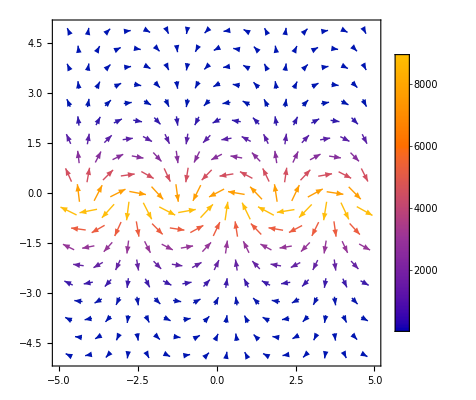

```mathematica
VectorPlot[{(Re[u1khrtin[rho1,rho2,U1in,U2in,g,k,x,z,0]])*UnitStep[z]+(Re[u2khrtin[rho1,rho2,U1in,U2in,g,k,x,z,0]])*UnitStep[-z]*Sign[-z],Re[w1khrtin[rho1,rho2,U1in,U2in,g,k,x,z,0]*UnitStep[z]+w2khrtin[rho1,rho2,U1in,U2in,g,k,x,z,0]*UnitStep[-z]*Sign[-z]]},{x,-5,5},{z,-5,5},PlotLegends->Automatic, VectorScaling->Automatic]
```

```mathematica
Manipulate[VectorPlot[{(Re[u1khrtin[rho1,rho2,U1in,U2in,g,k,x,z,t]])*UnitStep[z]+(Re[u2khrtin[rho1,rho2,U1in,U2in,g,k,x,z,t]])*UnitStep[-z]*Sign[-z],Re[w1khrtin[rho1,rho2,U1in,U2in,g,k,x,z,t]*UnitStep[z]+w2khrtin[rho1,rho2,U1in,U2in,g,k,x,z,t]*UnitStep[-z]*Sign[-z]]},{x,-5,5},{z,-5,5},PlotLegends->Automatic, VectorScaling->Automatic],{t,0,0.0001}]
```

## If we wish to look at the pure versions of these instabilities we can change our parameters to remove the presence of one of the two instabilities. First we look at the pure RT instability (Constant fluid density)

```mathematica
VideoGenerator[Rasterize@VectorPlot[{(U1in+Re[u1khrtin[rho1,rho2,U1in,U1in,g,k,x,z,#/2]])*UnitStep[z]+(U2in+Re[u2khrtin[rho1,rho2,U1in,U1in,g,k,x,z,#/2]])*UnitStep[-z]*Sign[-z],Re[w1khrtin[rho1,rho2,U1in,U1in,g,k,x,z,#/2]*UnitStep[z]+w2khrtin[rho1,rho2,U1in,U1in,g,k,x,z,#/2]*UnitStep[-z]*Sign[-z]]},{x,-5,5},{z,-5,5},PlotLegends->BarLegend[{Automatic,{0,30000}}],VectorColorFunctionScaling->False,VectorColorFunction->ColorData[{"Rainbow",{0,30000}}],VectorRange->{0,30000}]&,8,RasterSize->{500,500},BitRate->10 Quantity[, ("Megabits")/("Seconds")],FrameRate->60]//Parallelize
```

$Aborted

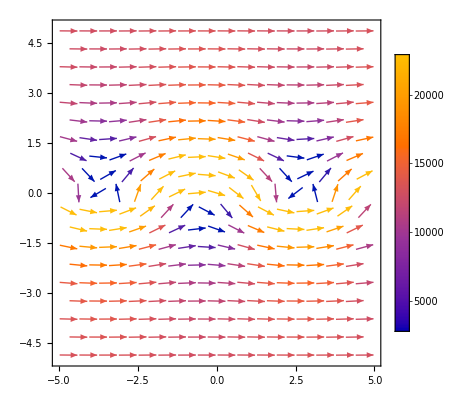

```mathematica
VectorPlot[{(U1in+Re[u1khrtin[rho1,rho2,U1in,U1in,g,k,x,z,3.5]])*UnitStep[z]+(U1in+Re[u2khrtin[rho1,rho2,U1in,U1in,g,k,x,z,3.5]])*UnitStep[-z]*Sign[-z],Re[w1khrtin[rho1,rho2,U1in,U1in,g,k,x,z,3.5]*UnitStep[z]+w2khrtin[rho1,rho2,U1in,U1in,g,k,x,z,3.5]*UnitStep[-z]*Sign[-z]]},{x,-5,5},{z,-5,5},PlotLegends->Automatic]
```

```mathematica
Manipulate[VectorPlot[{(U1in+Re[u1khrtin[rho1,rho2,U1in,U1in,g,k,x,z,t]])*UnitStep[z]+(U1in+Re[u2khrtin[rho1,rho2,U1in,U1in,g,k,x,z,t]])*UnitStep[-z]*Sign[-z],Re[w1khrtin[rho1,rho2,U1in,U1in,g,k,x,z,t]*UnitStep[z]+w2khrtin[rho1,rho2,U1in,U1in,g,k,x,z,t]*UnitStep[-z]*Sign[-z]]},{x,-5,5},{z,-5,5},PlotLegends->Automatic],{t,0,5}]
```

Looking at only the perturbations we have

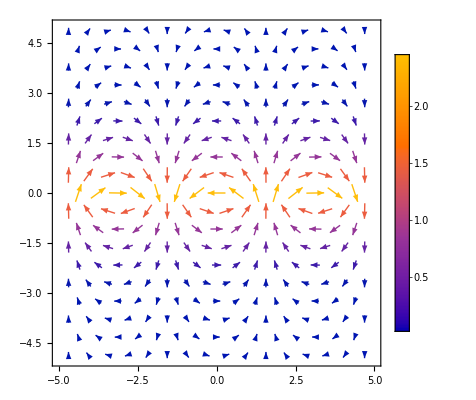

```mathematica
VectorPlot[{(Re[u1khrtin[rho1,rho2,U1in,U1in,g,k,x,z,0]])*UnitStep[z]+(Re[u2khrtin[rho1,rho2,U1in,U1in,g,k,x,z,0]])*UnitStep[-z]*Sign[-z],Re[w1khrtin[rho1,rho2,U1in,U1in,g,k,x,z,0]*UnitStep[z]+w2khrtin[rho1,rho2,U1in,U1in,g,k,x,z,0]*UnitStep[-z]*Sign[-z]]},{x,-5,5},{z,-5,5},PlotLegends->Automatic, VectorScaling->Automatic]
```

## Looking at the pure KH instability we have

```mathematica
VideoGenerator[Rasterize@VectorPlot[{(U1in+Re[u1khrtin[rho1in,rho2in,U1in,U2in,g,k,x,z,#/10000]])*UnitStep[z]+(U2in+Re[u2khrtin[rho1in,rho2in,U1in,U2in,g,k,x,z,#/10000]])*UnitStep[-z]*Sign[-z],Re[w1khrtin[rho1in,rho2in,U1in,U2in,g,k,x,z,#/10000]*UnitStep[z]+w2khrtin[rho1in,rho2in,U1in,U2in,g,k,x,z,#/10000]*UnitStep[-z]*Sign[-z]]},{x,-5,5},{z,-5,5},PlotLegends->BarLegend[{Automatic,{0,30000}}],VectorColorFunctionScaling->False,VectorColorFunction->ColorData[{"Rainbow",{0,30000}}],VectorRange->{0,30000}]&,10,RasterSize->{500,500},BitRate->5 Quantity[, ("Megabits")/("Seconds")],FrameRate->30]//Parallelize
```

```mathematica
Manipulate[VectorPlot[{(U1in+Re[u1khrtin[rho1in,rho2in,U1in,U2in,g,k,x,z,t]])*UnitStep[z]+(U2in+Re[u2khrtin[rho1in,rho2in,U1in,U2in,g,k,x,z,t]])*UnitStep[-z]*Sign[-z],Re[w1khrtin[rho1in,rho2in,U1in,U2in,g,k,x,z,t]*UnitStep[z]+w2khrtin[rho1in,rho2in,U1in,U2in,g,k,x,z,t]*UnitStep[-z]*Sign[-z]]},{x,-5,5},{z,-5,5},PlotLegends->Automatic, VectorScaling->Automatic],{t,0,0.001}]
```

Now looking at just the perturbations we have

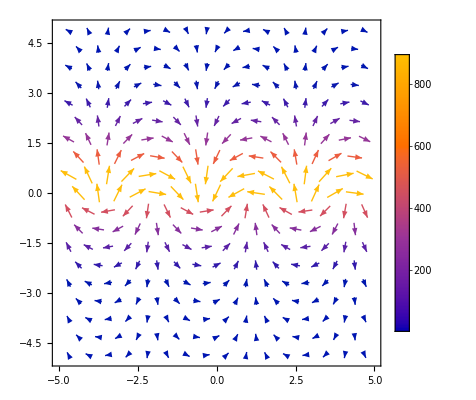

```mathematica
VectorPlot[{(Re[u1khrtin[rho1in,rho2in,1000,2000,g,k,x,z,0]])*UnitStep[z]+(Re[u2khrtin[rho1in,rho2in,1000,2000,g,k,x,z,0]])*UnitStep[-z]*Sign[-z],Re[w1khrtin[rho1in,rho2in,1000,2000,g,k,x,z,0]*UnitStep[z]+w2khrtin[rho1in,rho2in,1000,2000,g,k,x,z,0]*UnitStep[-z]*Sign[-z]]},{x,-5,5},{z,-5,5},PlotLegends->Automatic, VectorScaling->Automatic]
```

```mathematica
Manipulate[VectorPlot[{(Re[u1khrtin[rho1in,rho2in,1000,2000,g,k,x,z,t]])*UnitStep[z]+(Re[u2khrtin[rho1in,rho2in,1000,2000,g,k,x,z,t]])*UnitStep[-z]*Sign[-z],Re[w1khrtin[rho1in,rho2in,1000,2000,g,k,x,z,t]*UnitStep[z]+w2khrtin[rho1in,rho2in,1000,2000,g,k,x,z,t]*UnitStep[-z]*Sign[-z]]},{x,-1,1},{z,-1,1},PlotLegends->Automatic, VectorScaling->Automatic],{t,0,0.001}]
```

```mathematica
Manipulate[VectorPlot[{(Re[u1khrtin[rho1in,rho2in,U1in,U2in,g,k,x,z,t]])*UnitStep[z]+(Re[u2khrtin[rho1in,rho2in,U1in,U2in,g,k,x,z,t]])*UnitStep[-z]*Sign[-z],Re[w1khrtin[rho1in,rho2in,U1in,U2in,g,k,x,z,t]*UnitStep[z]+w2khrtin[rho1in,rho2in,U1in,U2in,g,k,x,z,t]*UnitStep[-z]*Sign[-z]]},{x,-1,1},{z,-1,1},PlotLegends->Automatic, VectorScaling->Automatic],{t,0,0.001}]
```

Now we look at the incompressible cases with exponentially varying density. First pure RT.

In the case of exponentially varying density we have that

ρ_i=(ρ̂)_i e^((-g (ρ̂)_i z)/P)=(ρ̂)_i e^((-g z)/c_i^2)=(ρ̂)_i e^(-z/L_i)

This leads to the perturbed velocity in z to be,

```mathematica
w1d=A e^(q1 z);
w2d = A e^(q2 z);
```

where the q’s are the solution to the following

```mathematica
Solve[q^2-q/L-K^2(1+G^2/(c^2 γ^2))==0,q]
```

{{q→1/2 (1/L-√(4 K^2+1/L^2+(4 G^2 K^2)/(c^2 γ^2)))},{q→1/2 (1/L+√(4 K^2+1/L^2+(4 G^2 K^2)/(c^2 γ^2)))}}

The functions for the velocities and densities would then be

```mathematica
w1drt[rho1_,rho2_,P_,g_,k_,x_,z_,t_]:=Exp[(1/2 (1/(Lfun[)+√(4 K^2+1/L^2+(4 G^2 K^2)/(c^2 γ^2)))]
```